-Graphics-
Image source: Roadside Wolfram Language

# Introduction to Wolfram Language

Jozsef Konczer

@ Milestone Institute

## Installation Help

Requirements:

https://www.wolfram.com/mathematica/system-requirements.html

Depending on the OS you use you have to download:

Linux: Mathematica_version_..._.sh

Mac: Mathematica_version_..._.dmg

Windows: Mathematica_version_..._.exe

Installation:

Mac, Windows:

double click on the installer, select folders for installation and scripts

Linux:

possibly prepare an installation folder

make the .sh script runable ($ chmod 755)

run it in terminal ($ /.  Mathematica_..._.sh)

select the installation folder (or default) during installation

(there is no problem, if you install the scripts into the same folder)

Activation:

Mac, Windows:

Open Mathematica

Enter Activation key

Linux:

Open Mathematica (run InstallationFolder/Executable/Mathematica)

Enter Activation key

### Wolfram Cloud

If something goes wrong, or you just want to use an Online version without installation you can create an account:

https://www.wolframcloud.com/

Here select “New Notebook” where you can start to Explore the Language.

## Introduction

```mathematica
2+3
```

5

### First aid Info

Running a command:

```mathematica
Text[Style["⇧ ⌤",FontSize->100]]
Text[Style["⇧ ↵",FontSize->100]]
```

⇧ ⌤

⇧ ↵

Accessing the Help: F1

```mathematica
?Sin
```

```mathematica
??Sin
```

General notation:

Function brackets: f[...]

```mathematica
Sin[1.]
```

0.841471

Built in functions star with capital letters: Sin[...], Join[...]

Lists: {...}

```mathematica
Join[{1,2},{3,4}]
```

{1,2,3,4}



```mathematica
Plot[x^2,{x,-2,2}]
```

List part: {...}[[2]]

```mathematica
{11,12,13}[[2]]
```

12

Numeric 2. or N[...]

```mathematica
Sin[1]
```

Sin[1]

```mathematica
Sin[1.]
```

0.841471

```mathematica
N[Sin[1]]
```

0.841471

Multiplication: 3 * 4 or 3 4, Power 3^4

```mathematica
3*4
```

12

```mathematica
3 4
```

12

```mathematica
3^4
```

81

“=” Sets a value for a variable, “==”  Test equality

```mathematica
a=5
```

5

```mathematica
a
```

5

```mathematica
4==2 2
```

True

### Basic Examples

```mathematica
50!
```

30414093201713378043612608166064768844377641568960512000000000000

```mathematica
N[2^(1/2),100]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573

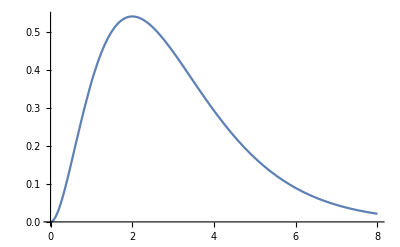

```mathematica
Plot[Exp[-x] x^2,{x,0,8}]
```

```mathematica
Manipulate[
Plot[Exp[-λ x] x^2,{x,0,8}],
{λ,1/2,2}]
```

```mathematica
Solve[x^2+5 x ==6,x]
```

{{x→-6},{x→1}}

```mathematica
Solve[{x+5 y==6,2 x+6 y==10},{x,y}]
```

{{x→7/2,y→1/2}}

```mathematica
FindRoot[Exp[-x] x^2==x/10,{x,2}]
```

{x→3.57715}

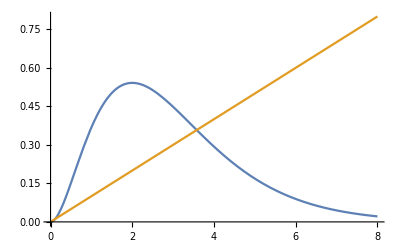

```mathematica
Plot[{Exp[-x] x^2,x/10},{x,0,8}]
```

```mathematica
Expand[(x-3)(x+2)(x-1)]
```

6-5 x-2 x^2+x^3

```mathematica
D[Exp[-x] x^2,x]
```

2 ⅇ^-x x-ⅇ^-x x^2

```mathematica
Simplify[2 ⅇ^-x x-ⅇ^-x x^2]
```

-ⅇ^-x (-2+x) x

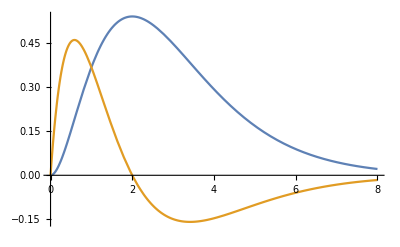

```mathematica
Plot[{Exp[-x] x^2,Evaluate[D[Exp[-x] x^2,x]]},{x,0,8}]
```

```mathematica
∫_2^6 Exp[-x] x^2ⅆx
```

(10 (-5+ⅇ^4))/ⅇ^6

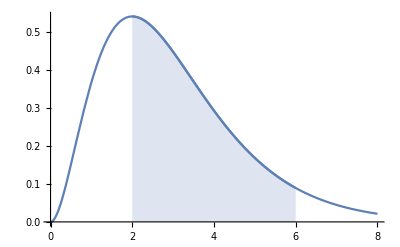

```mathematica
Show[
Plot[Exp[-x] x^2,{x,0,8}],
Plot[Exp[-x] x^2,{x,2,6},PlotRange->{0,All},Filling->Bottom]
]
```

```mathematica
NIntegrate[Exp[-x] x^2,{x,2,6}]
```

1.22942

```mathematica
table1=Table[N[Sin[k]],{k,1,10}]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}

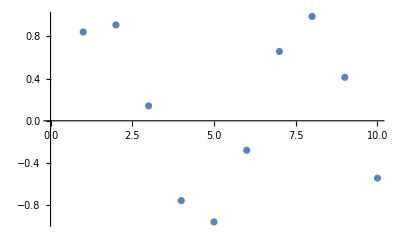

```mathematica
ListPlot[table1]
```

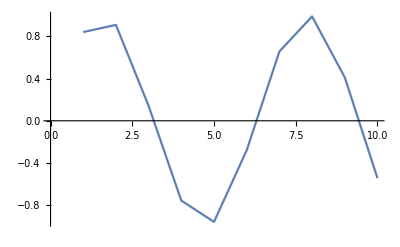

```mathematica
ListLinePlot[table1]
```

```mathematica
table1[[1]]
```

0.841471

```mathematica
table1[[2;;4]]
```

{0.909297,0.14112,-0.756802}

```mathematica
table1[[-1]]
```

-0.544021

```mathematica
Length[table1]
```

10

```mathematica
Total[table1]
```

1.41119

```mathematica
Mean[table1]
```

0.141119

```mathematica
Variance[table1]
```

0.533587

```mathematica
StandardDeviation[table1]
```

0.730471

```mathematica
table2=Table[2 k+3 + RandomReal[NormalDistribution[]],{k,1,10}]
```

{4.80016,7.26548,9.33187,9.5194,13.4979,15.2505,18.3509,18.5053,22.6666,22.3805}

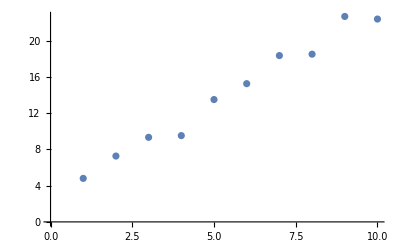

```mathematica
ListPlot[table2]
```

```mathematica
fittedmodel=NonlinearModelFit[table2,{α x+β},{α,β},x]
```

FittedModel[2.81868+2.06149 x]

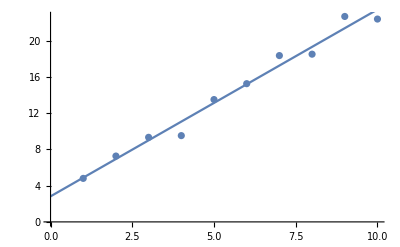

```mathematica
Show[
ListPlot[table2],
Plot[fittedmodel["BestFit"],{x,0,10}]
]
```

```mathematica
Plot3D[Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

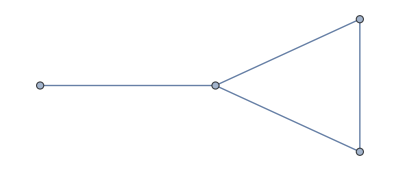

```mathematica
Graph[{"A"<->"B","B"<->"C","C"<->"A","A"<->"D"}]
```

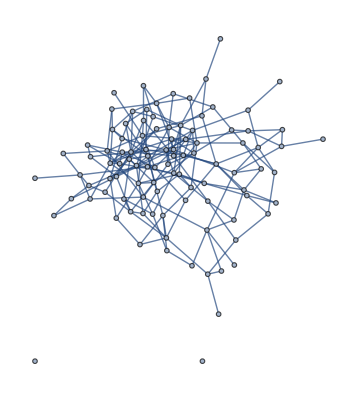

```mathematica
randomgraph=RandomGraph[{100,200}]
```

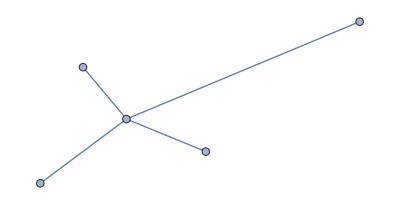

```mathematica
NeighborhoodGraph[randomgraph,1,1]
```

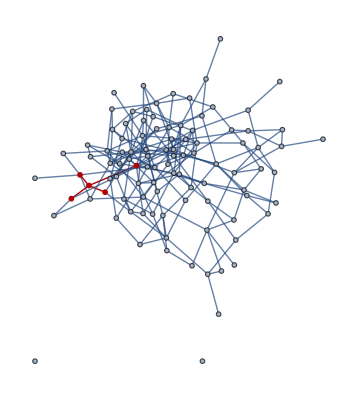

```mathematica
HighlightGraph[randomgraph,NeighborhoodGraph[randomgraph,1,1]]
```

```mathematica
matrix=Table[i-j,{i,1,5},{j,1,5}]
```

{{0,-1,-2,-3,-4},{1,0,-1,-2,-3},{2,1,0,-1,-2},{3,2,1,0,-1},{4,3,2,1,0}}

```mathematica
MatrixForm[matrix]
```

(0 | -1 | -2 | -3 | -4
1 | 0 | -1 | -2 | -3
2 | 1 | 0 | -1 | -2
3 | 2 | 1 | 0 | -1
4 | 3 | 2 | 1 | 0)

```mathematica
MatrixForm[matrix.matrix]
```

(-30 | -20 | -10 | 0 | 10
-20 | -15 | -10 | -5 | 0
-10 | -10 | -10 | -10 | -10
0 | -5 | -10 | -15 | -20
10 | 0 | -10 | -20 | -30)

```mathematica
matrix.{1,2,3,4,5}
```

{-40,-25,-10,5,20}

```mathematica
Dimensions[matrix]
```

{5,5}

```mathematica
Det[matrix]
```

0

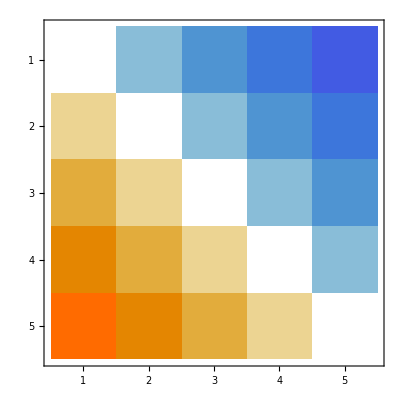

```mathematica
MatrixPlot[matrix]
```

### Variables and Functions

```mathematica
a=5
```

5

```mathematica
b=7;
```

```mathematica
c=RandomReal[]
```

0.253801

```mathematica
c
```

0.253801

```mathematica
d:=RandomReal[]
```

```mathematica
d
```

0.882531

```mathematica
d
```

0.892476

```mathematica
f[x_]=x^2 +RandomReal[]
```

0.0885326+x^2

```mathematica
f[u]
```

0.0885326+u^2

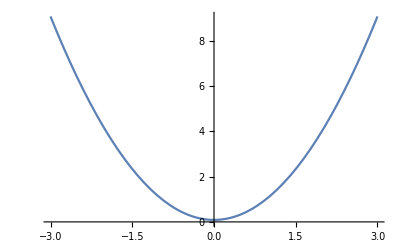

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
g[x_]:=x^2+ RandomReal[]
```

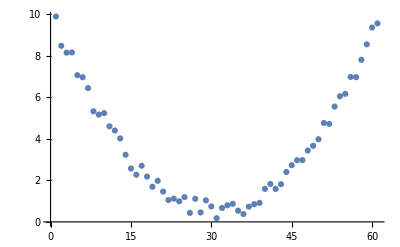

```mathematica
ListPlot[Table[g[x],{x,-3,3,0.1}]]
```

```mathematica
f[3]
f@3
3//f
f[x]/.x->3
```

9.08853

9.08853

9.08853

«1 more identical outputs»

```mathematica
h[x_,y_]:=x^2+y^2-x^2 y^2/3
```

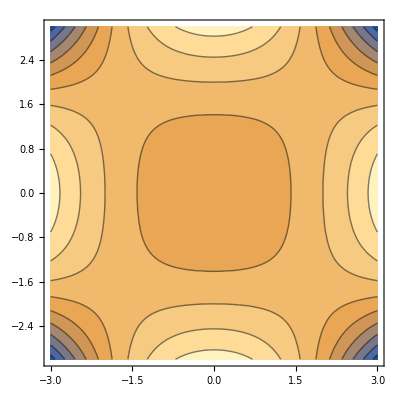

```mathematica
ContourPlot[h[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
ff[x_][y_]:=x^y
```

```mathematica
ff[2][3]
```

8

```mathematica
puref=(#^2+RandomReal[])&
```

#1^2+RandomReal[]&

```mathematica
puref[3]
```

9.42434

### Rules, Patterns Replacement

```mathematica
rule=x->5
```

x→5

```mathematica
{x,x,y,z}/.rule
```

{5,5,y,z}

```mathematica
x Exp[x]/.x->3
```

3 ⅇ^3

```mathematica
{a,b,{c,d}}/.{x_,y_}:>x^y
```

{a,b,c^d}

```mathematica
Nest[#/.x_:>1/(1+x)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Simplify[Nest[#/.x_:>1/(1+x)&,x,10]]
```

(55+34 x)/(89+55 x)

```mathematica
1.//.x_:>1/(1+x)
```

0.618034

## Advanced material

### Structure and Philosophy

In Wolfram Language everything is an expression:

Atomic expressions are expressions:

Numbers

Integers (1, 2, 3, ...)

Rational (1/2, 1/3, 3/2 ...)

Complex (4+2 I)

Floating-point numbers (2.45)

Symbols

Variable/Function names (x, y, ...)

Built in functions (Sin, Cos, ...)

Strings

“a”, “b”, “abc”

Other

SparseArray

Tree

...

Any f[expr1, expr2, ...] is an expression

```mathematica
FullForm[Sin[2+x]]
```

Sin[Plus[2,x]]

Head:

If we have an expression expr = f[expr1, expr2, ...]

Head[expr] gives f

If an expression is Atomic, it gives “Integer”, “Symbol”, “String” etc.

AtomQ

gives True if the expression is atomic, and False otherwise.

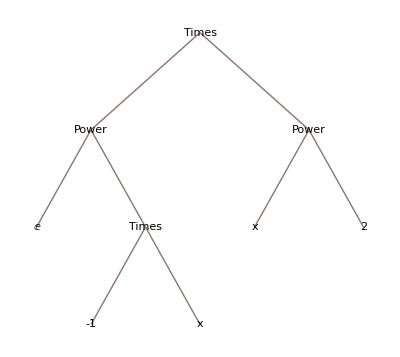

```mathematica
TreeForm[Exp[-x] x^2]
```

Evaluation means Pattern Matching:

Under the hood in Wolfram Language everything is Pattern Matching

```mathematica
product[x,1+x]/.product[a_,b_+c_]:>product[a,b]+product[a,c]
```

product[x,1]+product[x,x]

Pattern Matching starts from the Head, and then moves to the subexpressions until no more replacement can be done

```mathematica
G[1]=1;
G[_]=2;
TraceScan[Print,G[G[1]]]
```

G[G[1]]

G

G[1]

G

1

1

G[1]

1

1

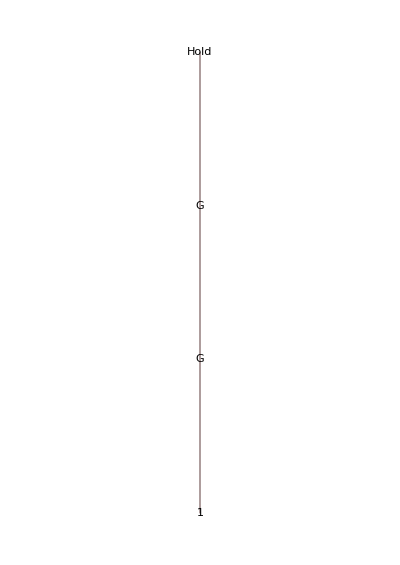

```mathematica
TreeForm[Hold[G[G[1]]]]
```

The result of ReplaceAll can be different, because: “looks at each part of expr, tries all the rules on it, and then goes on to the next part of expr. The first rule that applies to a particular part is used; no further rules are tried on that part or on any of its subparts. ”

```mathematica
F[F[1]]/.{F[1]->1,F[_]->2}
```

2

Patterns are ordered

```mathematica
{F[2],F[4],F[1,2]}/.{F[4]->9,F[x_]:>x^2,F[__]:>0}
```

{4,9,0}

```mathematica
{F[2],F[4],F[1,2]}/.{F[x_]:>x^2,F[4]->9,F[__]:>0}
```

{4,16,0}

```mathematica
{F[2],F[4],F[1,2]}/.{F[__]:>0,F[4]->9,F[x_]:>x^2}
```

{0,0,0}

Function definition is essentially a pattern definition:

```mathematica
g[x_]:=x^2
```

```mathematica
g[4]
```

16

If there are multiple patterns for a function, they are ordered from “more specific” to “more general”:

```mathematica
Clear[g]
g[x_]:=x^2
g[4]=9;
g[__]=0;
```

```mathematica
{g[2],g[4],g[1,2]}
```

{4,9,0}

```mathematica
?g
```

```mathematica
Clear[h1]
h1[x_,1]:=1
h1[1,x_]:=2
h1[2,2]:=3
```

```mathematica
Clear[h2]
h2[1,x_]:=2
h2[x_,1]:=1
h2[2,2]:=3
```

```mathematica
?h1
```

```mathematica
?h2
```

```mathematica
h1[1,1]
```

1

```mathematica
h2[1,1]
```

2

### Effective List operations

```mathematica
list1=RandomVariate[NormalDistribution[0,5],100]
```

{-6.87355,-2.73391,6.18157,3.48944,4.10168,-1.6472,-4.7907,9.71854,-2.20636,2.51035,1.45401,3.15169,-4.69462,6.054,5.09533,-5.25156,9.27122,-0.898054,-2.87964,7.65583,-5.40525,-2.65573,-1.60787,-2.00904,-5.36524,5.62626,-0.324661,1.77732,-4.61591,9.08727,-1.34813,-3.68845,-1.30712,0.197777,-4.3606,-0.348494,0.745437,-2.19665,2.32561,5.97216,-3.11106,-0.310734,-5.14353,-4.87375,-7.5661,-5.91909,7.62014,-0.464339,8.77918,5.78627,9.78105,-2.60334,-1.88843,1.08888,-0.699048,3.80507,-14.6474,0.765851,-7.24317,-4.49042,1.4425,0.511106,4.06928,-9.04674,2.69308,0.431537,1.41956,17.8916,2.60851,-1.55566,-2.41142,2.61496,-4.32458,7.28566,-6.06807,1.08544,-3.47043,-5.10416,1.56527,-4.84961,3.02098,-6.45865,-6.03916,5.6033,6.01395,-7.41693,-2.49795,1.94418,3.41561,-4.42325,-0.0237302,-5.66042,4.80256,-3.60453,1.00694,3.76432,-1.09665,-8.22991,-8.89274,-4.38049}

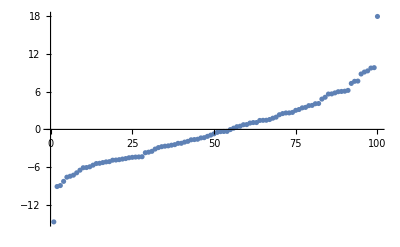

```mathematica
ListPlot[list2=Sort[list1]]
```

```mathematica
list3=Sin/@list2;
```

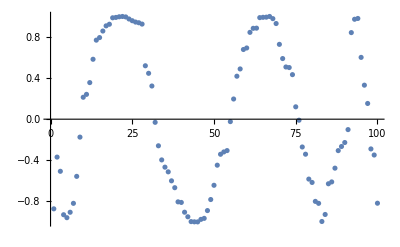

```mathematica
ListPlot[list3]
```

```mathematica
RepeatedTiming[(1-#)^2&/@list2]//Short
```

{8.48967×10^-6,{244.841,«19»,«97»,«19»}}

```mathematica
RepeatedTiming[
Table[(1-list2[[k]])^2,{k,1,Length[list2]}]
]//Short
```

{0.0000628135,{244.841,«19»,«96»,«18»,«19»}}

```mathematica
RepeatedTiming[Transpose[{list2,list3}]]//Short
```

{1.12023×10^-6,{«1»}}

```mathematica
RepeatedTiming[
Table[{list2[[k]],list3[[k]]},{k,1,Length[list2]}]
]//Short
```

{0.0000547688,{{-14.6474,-«19»},«98»,{«1»}}}

```mathematica
{Min[list1],Max[list1],MinMax[list1]}
```

{-14.6474,17.8916,{-14.6474,17.8916}}

```mathematica
list1.list1
```

2683.09

```mathematica
Norm[list1]
```

51.7986

### Monitoring

```mathematica
Monitor[Table[Pause[0.05],{k,1,100}],k]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Monitor[Table[Pause[0.05],{k,1,100}],ProgressIndicator[k,{1,100}]];
```

### Module, Block, With

```mathematica
somefunction[x_List]:=Module[
{y},
y=1;
Table[
y=y x[[k]]
,{k,1,Length[x]}]
]
```

```mathematica
somefunction[{2,3,4}]
```

{2,6,24}

Block similar, and a little faster.

```mathematica
RepeatedTiming[With[{a=5},Exp[a x] x]]
```

{1.67821×10^-6,ⅇ^(5 x) x}

```mathematica
RepeatedTiming[Exp[a x] x/.a->5]
```

{3.44247×10^-6,ⅇ^(5 x) x}

### Loops: For, While, Do

Available, but not encouraged

```mathematica
For[i=0,i<4,i++,
Print[i]
]
```

0

1

2

3

```mathematica
n=1;
While[n<4,
Print[n];
n++
]
```

1

2

3

### Entities

```mathematica
hu=Entity["Country","Hungary"]
```

Hungary

```mathematica
hu["Properties"]//Shallow
```

{active home listings,adjusted net national income,seasonal bank borrowings from Fed, plus adjustments,regions,adult population,obese adults,number of aggravated assaults,rate of aggravated assault,aggregate home value,aggregate home value, householder 15 to 24 years,«751»}

```mathematica
hu[EntityProperty["Country","AdultPopulation"]]
```

6.3791×10^6 people

### Development tools

#### Namespace Management

```mathematica
$Context
```

Global`

```mathematica
Begin["MyContext`"];
square[x_]:=x^2
End[];
```

```mathematica
MyContext`square[6]
```

36

```mathematica
Contexts[]//Short
```

{Algebra`,Algebraics`Private`,«1534»,XML`SVG`,$CellContext`}

#### Options

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
Options[f]={a->a0,b->b0};
f[x_,OptionsPattern[]]:={x,OptionValue[a]}
f[7,a->uuu]
```

{7,uuu}

#### Error handling

```mathematica
{Message,Quiet,$Failed}
```

## Further introductory materials and References

An Elementary Introduction to the Wolfram Language

https://www.wolfram.com/language/elementary-introduction/2nd-ed/

Mathematica Summer School on Theoretical Physics

http://msstp.org/

Wolfram Language & System Documentation Center

https://reference.wolfram.com/language/tutorial/IntroductionOverview.html

LaTeX typesetting in Mathematica

http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html

Forums:

https://mathematica.stackexchange.com/

https://community.wolfram.com/

## Computational view on WL

Symbols Graph in Mathematica 1

```mathematica
Short[symbolEntityList=EntityList[EntityClass["WolframLanguageSymbol","VersionIntroduced"->1]]]
```

{Above,Abs,Accuracy,AccuracyGoal,AddTo,AiryAi,All,And,Apart,Append,AppendTo,Apply,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinh,ArcTan,ArcTanh,Arg,ArithmeticGeometricMean,Array,AspectRatio,AtomQ,Attributes,«494»,ViewPoint,WeierstrassP,WeierstrassPPrime,Which,While,WorkingPrecision,Write,WriteString,Xor,ZeroTest,Zeta,$CommandLine,$Context,$ContextPath,$Display,$DisplayFunction,$Echo,$Epilog,$IgnoreEOF,$Line,$Messages,$Output,$Path,$Post,$Pre,$PrePrint,$RecursionLimit,$System,$Urgent,$Version}

```mathematica
Short[relatednessList={#,Intersection[#["RelatedSymbols"],symbolEntityList]}&/@symbolEntityList]
```

{{Above,{Below,Center,Top}},{Abs,{Arg,Conjugate,Im,Mod,Re,Sign}},{Accuracy,{AccuracyGoal,Chop,N,Precision,WorkingPrecision}},{AccuracyGoal,{Accuracy,Precision,WorkingPrecision}},«547»,{$System,{$Version}},{$Urgent,{$Echo,$Output}},{$Version,{$System}}}

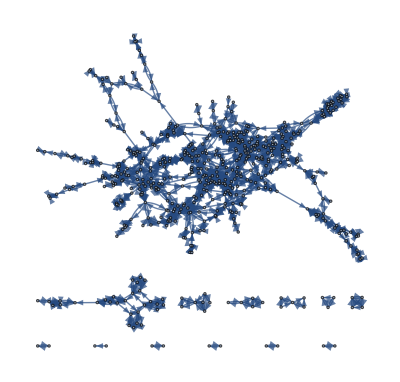

```mathematica
Graph[Flatten[Thread[#[[1]]->#[[2]]]&/@relatednessList],VertexLabels->Placed["Name",Tooltip]]
```

Current Symbol list is much longer:

```mathematica
Short[EntityList["WolframLanguageSymbol"]]
```

{$Aborted,$ActivationKey,$AllowDataUpdates,$AllowExternalChannelFunctions,$AllowInternet,$AssertFunction,$Assumptions,$AudioDecoders,$AudioEncoders,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BasePacletsDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudAccountName,$CloudBase,$CloudConnected,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudObjectNameFormat,$CloudObjectURLType,«6086»,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,XYZColor,Xnor,Xor,Yellow,Yesterday,YuleDissimilarity,ZIPCodeData,ZTest,ZTransform,ZernikeR,ZeroSymmetric,ZeroTest,Zeta,ZetaZero,ZipfDistribution,ZoomCenter,ZoomFactor}

```mathematica
SetDirectory[$InstallationDirectory<>"/Documentation/English/System/ReferencePages/Symbols/"];
FileNames[]//Length
```

6330

See also:

```mathematica
WolframLanguageData[]
```